```mathematica
Solve[2x^2-x-6==0,x]
```

{{x→-3/2},{x→2}}

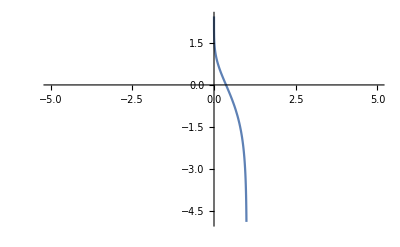

```mathematica
Plot[Log[Log[1/x]],{x,-5,5}]
```

```mathematica
Expand[2(x-3/2)(x+2)]
```

-6+x+2 x^2

x<0||0<x<3/2||3/2<x<2||x>2

1<x<3/2||3/2<x<2||2<x<ⅇ||x>ⅇ

0<x<1/2||1/2<x<3/2||3/2<x<2||2<x<3||x>3

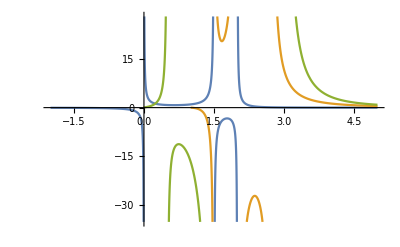

{{1.93459,-3.38469,0.214737,0.0613876,0.0015361},{-1.19015,23.1364,-31.4439,20.2145,0.483141},{-44.8775,176.825,-57.3805,-118.351,0.892505}}

```mathematica
den=2x^2-7x+6;
p=(1/(2^x-1))/den;
q=((3Log[x])/(Log[Log[x]]))/den;
g=(9Sqrt[x+1]/(Log[2x]Log[x/3]))/den;

d1=FunctionDomain[p,x]//Reduce
d2=FunctionDomain[q,x]//Reduce
d3=FunctionDomain[g,x]//Reduce

Plot[{p,q,g},{x,-2,5}]
{p,q,g}/.{x->{1.25,7/4,2.5,2.9,5}}//N
```

```mathematica
Solve[2x^2-7x+6==0,x]
```

{{x→3/2},{x→2}}

```mathematica
D[Log[Exp[x] Sin[x]],x]
```

ⅇ^-x Csc[x] (ⅇ^x Cos[x]+ⅇ^x Sin[x])

```mathematica
Exp[Integrate[ⅇ^-x Csc[x] (ⅇ^x Cos[x]+ⅇ^x Sin[x]),x]]
```

ⅇ^x Sin[x]

```mathematica
D[x,{x,2}]-D[-Cos[x],{x,1}]+Sin[x]
```

0

```mathematica
DSolve[Integrate[D[P[x] D[y[x],x],x]+D[f[x] y[x],x],x]==Integrate[0,x],y[x],x]
```

{{y[x]→ⅇ^(∫_1^x -f[K[1]]/P[K[1]]ⅆK[1]) C[1]}}

```mathematica
ClearAll[A,B,c,x,Y]
Y=(A x^2+B x + c)Exp[3x];
D[Y,{x,2}]+9Y//Expand
Y2=Y/.{A->1/18,B->-1/27,c->1/162}
D[Y2,{x,2}]+9Y2//Expand
Y3=Y2+2/3
D[Y3,{x,2}]+9Y3//Expand
```

2 A ⅇ^(3 x)+6 B ⅇ^(3 x)+18 c ⅇ^(3 x)+12 A ⅇ^(3 x) x+18 B ⅇ^(3 x) x+18 A ⅇ^(3 x) x^2

ⅇ^(3 x) (1/162-x/27+x^2/18)

ⅇ^(3 x) x^2

2/3+ⅇ^(3 x) (1/162-x/27+x^2/18)

6+ⅇ^(3 x) x^2

```mathematica
Solve[2/3+18B==0,B]
```

{{B→-1/27}}

```mathematica
Solve[-1/9+18c==0,c]
```

{{c→1/162}}

```mathematica
DSolve[y''[x]+2y'[x]+y[x]==2Exp[-x],y[x],x]
```

{{y[x]→ⅇ^-x x^2+ⅇ^-x C[1]+ⅇ^-x x C[2]}}

```mathematica
Y=A x^2 Exp[-x];
D[Y,{x,2}]+2 D[Y,{x,1}]+Y
Solve[%==2Exp[-x],A]
Y2=Y/.{A->%[[1,1,2]]}
D[Y2,{x,2}]+2 D[Y2,{x,1}]+Y2//FullSimplify
```

2 A ⅇ^-x-4 A ⅇ^-x x+2 A ⅇ^-x x^2+2 (2 A ⅇ^-x x-A ⅇ^-x x^2)

{{A→1}}

ⅇ^-x x^2

2 ⅇ^-x

```mathematica
DSolve[y''[x]+2y'[x]-3y[x]==4Sin[2x],y[x],x]
```

{{y[x]→ⅇ^(-3 x) C[1]+ⅇ^x C[2]-4/65 (4 Cos[2 x]+7 Sin[2 x])}}

```mathematica
DSolve[y''[x]-2y'[x]-2y[x]==2x+4x^3,y[x],x]
```

{{y[x]→25-19 x+6 x^2-2 x^3+ⅇ^((1-√3) x) C[1]+ⅇ^((1+√3) x) C[2]}}

```mathematica
DSolve[y''[x]+2y'[x]+y[x]==2Exp[-x],y[x],x]
```

{{y[x]→ⅇ^-x x^2+ⅇ^-x C[1]+ⅇ^-x x C[2]}}